```mathematica
ToExpression["a",TeXForm]
```

a

```mathematica
(*criticalRule = {ν->(Subscript[δ, c][M,z])^2/NIntegrate[(1/(2 π^2))σ[M,m,z],{k,0,∞}]}*)
omegaRules={Subscript[Ω, Λ,0]->0.75,Subscript[Ω, 0]->Subscript[Ω, Λ,0] + Subscript[Ω, m,0] + Subscript[Ω, τ,0],Subscript[Ω, τ,0]->4.2 10^-5/h^2,Subscript[Ω, m,0]->0.27}
rules={Subscript[a, 1]->3.4,Subscript[a, 2]->1.0,Subscript[a, 3]->1.8,Subscript[a, 4]->0.5,Subscript[a, 5]->1.7,Subscript[a, 6]->0.9,Subscript[Ω, b]->0.0493,Subscript[Ω, m]->0.3153,h->0.6736,Subscript[σ, 8]-> 0.8111,Subscript[n, s]->0.9649,Subscript[M, J]->(1.6348126556655486*^-25 Subscript[a, 1] Subscript[M, s] (h^2 Subscript[Ω, m])^(1/4))/(h m^(3/2)),Subscript[M, s]->1,ρ->1,A->1}(*m->10^-22*)
```

{Ω_(Λ,0)→0.75,Ω_0→Ω_(m,0)+Ω_(Λ,0)+Ω_(τ,0),Ω_(τ,0)→0.000042/h^2,Ω_(m,0)→0.27}

{a_1→3.4,a_2→1.,a_3→1.8,a_4→0.5,a_5→1.7,a_6→0.9,Ω_b→0.0493,Ω_m→0.3153,h→0.6736,σ_8→0.8111,n_s→0.9649,M_J→(1.63481×10^-25 a_1 M_s (h^2 Ω_m)^(1/4))/(h m^(3/2)),M_s→1,ρ→1,A→1}

```mathematica
Ee[z_]:=(Subscript[Ω, Λ,0]+(1-Subscript[Ω, 0])(1+z)^2+Subscript[Ω, m,0](1+z)^3+Subscript[Ω, τ,0](1+z)^4)^(1/2)
```

```mathematica
Subscript[Ω, Λ][z_]:= Subscript[Ω, Λ,0]/Ee[z]^2
Subscript[Ω, m][z_]:= (Subscript[Ω, m,0](1+z)^3)/Ee[z]^2
Subscript[Ω, τ][z_]:= (Subscript[Ω, τ,0](1+z)^4)/Ee[z]^2
g[z_]:=5/2 Subscript[Ω, m][z](Subscript[Ω, m][z]^(4/7)-Subscript[Ω, Λ][z]+(1+Subscript[Ω, m][z]/2)(1+Subscript[Ω, Λ][z]/70))^(-1)
De[z_]:=g[z]/(1+z)
```

Result of following equation pasted into G[M,m]

```mathematica
Subscript[h, F][x_]:=(1/2 (1-Tanh[Subscript[M, J](x-Subscript[a, 2])]))
Subscript[h, F][M/Subscript[M, J]]/.rules/.rules
Subscript[h, F][M/Subscript[M, J]] Exp[Subscript[a, 3](M/Subscript[M, J])^(-Subscript[a, 4])]+(1-Subscript[h, F][M/Subscript[M, J]]) Exp[Subscript[a, 5](M/Subscript[M, J])^(-Subscript[a, 6])]/.rules/.rules//FullSimplify
```

1/2 (1-Tanh[(5.07489×10^-25 (-1.+1.97049×10^24 m^(3/2) M))/m^(3/2)])

1/2 (-ⅇ^((2.31917×10^-22)/((m^(3/2) M)^0.9)) (-1+Tanh[(5.07489×10^-25)/m^(3/2)-1. M])+ⅇ^((1.28229×10^-12)/((m^(3/2) M)^0.5)) (1+Tanh[(5.07489×10^-25)/m^(3/2)-1. M]))

```mathematica
(*G[M_]:=1. ⅇ^(40549.54037451929/M^0.5)*)
```

```mathematica
G[M_,m_]:=1/2 (-ⅇ^((2.3191727356704216*^-22)/((m^(3/2) M)^0.9)) (-1+Tanh[(5.074892668471512*^-25)/m^(3/2)-0.9999999999999999 M])+ⅇ^((1.2822890565643808*^-12)/((m^(3/2) M)^0.5)) (1+Tanh[(5.074892668471512*^-25)/m^(3/2)-0.9999999999999999 M]))
```

```mathematica
Subscript[δ, crit][z_]:=1.686/De[z]
Subscript[δ, c][M_,m_,z_]:=G[M,m] Subscript[δ, crit][z]/.omegaRules/.omegaRules/.rules//FullSimplify
```

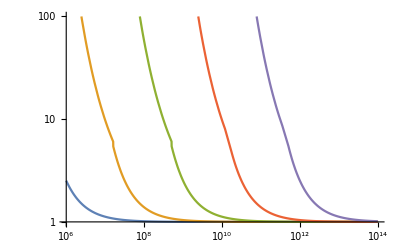

```mathematica
(*LogLogPlot[G[M],{M,10^6,10^14}]*)
LogLogPlot[Evaluate@Table[G[M,m],{m,{10^-20,10^-21,10^-22,10^-23,10^-24}}],{M,10^6,10^14},PlotRange->{1,100}]
```

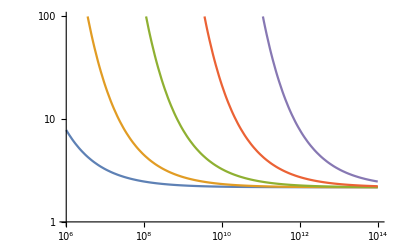

```mathematica
LogLogPlot[Evaluate@Table[Subscript[δ, c][M,y,0],{y,{10^-20,10^-21,10^-22,10^-23,10^-24}}],{M,10^6,10^14},PlotRange->{1,100}]
```

```mathematica
W[k_,R_]:=3/(k R)^3(-k R Cos[k R]+Sin[k R])
```

```mathematica
Subscript[T, F][k_,m_]:=Cos[x^3]/(1+x^8)/.x->1.61(Subscript[m, 22])^(1/18)k/kJ/.kJ->9(Subscript[m, 22])^(1/2)/.Subscript[m, 22]->m/10^-22
```

σ^2(M)==⟨δ_s^2(x;R)⟩==1/(2 π^2)∫_0^∞ P(k)(W̃)^2(kR)k^2 dk

```mathematica
Subscript[σ, integrand2][M_,m_,n_] := k^(n+2)(Subscript[T, F][k,m])^2(W[k,R])^2/.R->((3M)/(4π ρ))^(1/3)/.rules
```

```mathematica
Subscript[σ, integrand][M_,m_,n_] := k^(n+2)(Subscript[T, F][k,m])^2/.rules
```

```mathematica
(*f[ν_]:=(A e^(-(0.707ν)/2) (1+(0.707ν)^-0.3) √(0.707ν))/(ν √(2 π))*) 
(*ν = NIntegrate[(1/(2 π^2))σ[M,m,z],{k,0,∞}]*)
ν[M_,m_,z_]:=(Subscript[δ, c][M,m,z])^2/Integrate[(1/(2 π^2))Subscript[σ, integrand][M,m,1],{k,0,1/R/.R->((3M)/(4π ρ))^(1/3)/.rules}]
```

```mathematica
Integrate[(1/(2 π^2))Subscript[σ, integrand][M,m,1],{k,0,1/R/.R->((3M)/(4π ρ))^(1/3)/.rules}]
```

$Aborted

```mathematica
N[ν[10^6,10^-22,1]]
```

2.37911×10^45

Next expression has nu substituted explicitly

```mathematica
f[M_,m_,z_]:=(A e^(-(0.707ν[M,m,z])/2) (1+(0.707ν[M,m,z])^-0.3) √(0.707ν[M,m,z]))/(ν[M,m,z] √(2 π))/.rules
```

```mathematica
N[f[10^10,10^-22,8]]
```

(1.24279×10^-9)/(e^(2.57538×10^16))

```mathematica
fe[M_,m_,z_]:=(NIntegrate[(1/(2 π^2))Subscript[σ, integrand][M,m,1],{k,0,∞}] √(2 π))/(Subscript[δ, c][M,m,z])^2 A e^(-(0.707(Subscript[δ, c][M,m,z])^2)/(2NIntegrate[(1/(2 π^2))Subscript[σ, integrand][M,m,1],{k,0,∞}])) (1+(0.707(Subscript[δ, c][M,m,z])^2/NIntegrate[(1/(2 π^2))Subscript[σ, integrand][M,m,1],{k,0,∞}])^-0.3) √(0.707(Subscript[δ, c][M,m,z])^2/NIntegrate[(1/(2 π^2))Subscript[σ, integrand][M,m,1],{k,0,∞}])
```

```mathematica
(* n[M_,z_]:=(dν f[ν] Subscript[ρ̄, m])/(M dM)*)
```

```mathematica
NIntegrate[(1/(2 π^2))Subscript[σ, integrand][10,10^-22,1],{k,0,∞}]
```

6.34638

f(S)==A √(1/(2π))√q ν[1+(√q ν)^(-2p)]exp(-(q ν^2)/2)1/S

```mathematica
(*Subscript[P, lin]^FDM[k,z]==Subscript[P, lin]^CDM[k,z] (Subscript[T, F][k,m])^2*)
```

P_lin^FDM[k,z]==(7.06047×10^-64 cos^2 k^6 P_lin^CDM[k,z])/((1+(6.28702×10^-85 k^8)/m^(32/9))^2 m^(8/3))

```mathematica
(*Subscript[P, lin]^FDM[k_,z_]==k^n (Subscript[T, F][k,m])^2*)
```

```mathematica
n[M_,m_,z_]:=ρ fe[M,m,z]/.omegaRules/.omegaRules/.rules
```

```mathematica
LogLogPlot[NIntegrate[f[t,10^-22,8],{t,y,10^20}],{y,10^6,10^11},PlotRange->{10^3,10^10}]
```

NIntegrate::nlim: k = 1.61199/t^(1/3) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::inumr: The integrand 0.0221569 «4» NIntegrate[σ_integrand[t,1/(1000«14»00000),1]/(2 π^2),{k,0,1/R/.R→Times[«3»]^Times[«2»]/.{a_1→3.4,a_2→1.,«8»,«5»}}] has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.00024×10^6,100000000000000000000}}.

Power::infy: Infinite expression 1/0^(4/3) encountered.

Power::infy: Infinite expression 1/0^(32/9) encountered.

Power::infy: Infinite expression 1/0^(4/3) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::inumr: The integrand 0.0221569 «4» NIntegrate[σ_integrand[t,1.×10^-22,1]/(2 π^2),{k,0,1/R/.R→Times[«3»]^Times[«2»]/.{a_1→3.4,a_2→1.,«8»,«5»}}] has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.00024×10^6,1.×10^20}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

$Aborted

```mathematica
NIntegrate[f[u,10^-22,8],{u,10^6,10^8}]
```

$Aborted

```mathematica
NIntegrate[f[t,10^-22,8],{t,10^6,10^20}]
```

NIntegrate::inumr: The integrand (8 Cos[«22» «1»]^2 (-(k «2» «1»)/2^(«1»)+Sin[«1»])^2)/(k^3 (1+«22» k^8)^2 t^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

General::munfl: -2.22507×10^-308 (-2.22507×10^-308) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -2.22507×10^-308 2.22507×10^-308 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.22507×10^-308 (-2.22507×10^-308) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate[f[t,1/10^22,8],{t,10^6,10^20}]

```mathematica
LogLogPlot[Evaluate@Table[NIntegrate[n[x,10^-22,8],{x,M,∞}],{m,{10^-20,10^-21,10^-22,10^-23,10^-24}}],{M,10^6,10^14},PlotRange->{1,100}]
```